# Power Dissipation of Halmholtz Coil

```mathematica
(* all length in mm *)
```

```mathematica
(* copper resistivity *)
Res[temp_]:=Interpolation[{{1,0.002},{10,0.00202},{20,0.0028},
{40,0.0239},{60,0.0971},{80,0.215},{100,0.348},{150,0.699},{200,1.046},{273,1.543},{293,1.678},{298,1.712},{300,1.725},{400,2.402},{500,3.09},{600,3.792},{700,4.514},{800,5.262},{900,6.041}}][temp] 10^-8
(* Magnetic field of Halmholtz Coil , n = turn in each coil*)
BH[r_,I_,n_]:=(4/5)^(3/2)4π 10^-7 n I/(r/1000)
BS[r_,Δz_,I_,n_](* in mT*):= 4π 10^-7 (r/1000)^2/(((r/1000)^2+(Δz/2000)^2)^(3/2))n I 1000
```

```mathematica
Res[300]/Res[100]
```

4.9569

```mathematica
BS[15,30,8.44,12] //N
```

2.99983

```mathematica
Solve[BS[16.75,30, i, 12]==3, i]//N
```

{{i→8.06052}}

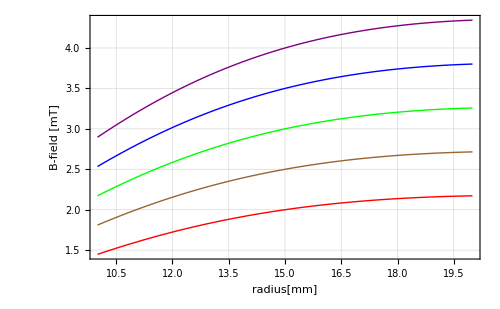

```mathematica
Plot[Evaluate[Table[BS[r,30,8.44,n],{n,8,16,2}]],{r,10,20},PlotRange->{0,All},PlotStyle->{Red, Brown, Green, Blue, Purple},
Frame->True, FrameLabel->{"radius[mm]", "B-field [mT]"},
Epilog->Text["I=8.44A, z=30mm, turn=8,10,12,14,16",{14,0.9}],
ImageSize-> 500, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

```mathematica
(* Resistance *)
R[n_,r_,d_,temp_]:=Res[temp](2 n) (2 π r/1000)/(π(d/2000)^2)
(* Power Dissiplation total *)
PI[I_,n_, r_, d_, temp_]:= I^2 R[n,r,d,temp]
PBS[B_,n_,r_,Δz_,d_, temp_]:=((625 B (4 r^2+Δz^2)^(3/2))/(2 n π r^2))^2 R[n,r,d,temp]
```

```mathematica
R[12,15,1,100]
PI[8.44,12,15,1,100]
PBS[0.003,12,15,30,1,100]
```

0.0100224

0.713932

0.71401

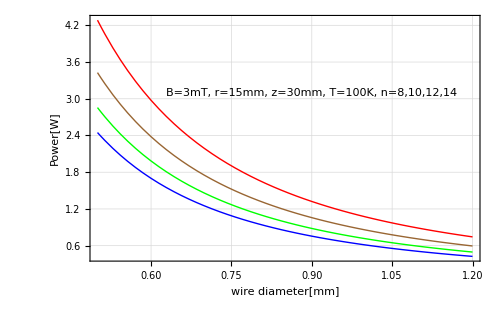

```mathematica
Plot[Evaluate[Table[PBS[0.003,n,15,30,d,100],{n,8,14,2}]],{d,0.5,1.2},PlotStyle->{Red, Brown, Green, Blue, Purple},
Frame->True, FrameLabel->{"wire diameter[mm]","Power[W]"},
Epilog->Text["B=3mT, r=15mm, z=30mm, T=100K, n=8,10,12,14",{0.9,3.1}],
ImageSize-> 500, GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

```mathematica
(* totoal length (* mm *) require *)
l[r_,i_]:=N[2((15 √2 √(r^2))/(i π) 2π r)+ 100 (* buffer *)]
```

```mathematica
l[15,20]
```

1054.59

```mathematica
(* Coil Thickness *)
CoilThick[d_,n_]:=√n d 1.6
```

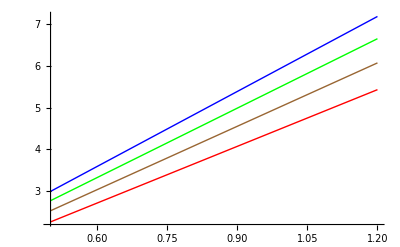

```mathematica
Plot[Evaluate[Table[CoilThick[d,n],{n,8,14,2}]],{d,0.5,1.2},PlotStyle->{Red, Brown, Green, Blue, Purple}]
```